```mathematica
resource=ResourceObject["MNIST"];
trainingData=RandomSample@ResourceData[resource,"TrainingData"];
testData=RandomSample@ResourceData[resource,"TestData"];
```

```mathematica
groupedTrainingData=#⟦500;;⟧&/@GroupBy[trainingData,Last->First];
groupedValidationData=#⟦;;500⟧&/@GroupBy[trainingData,Last->First];
groupedTestData=GroupBy[testData,Last->First];
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
Length@groupedTrainingData[#]&/@Range[0,9]//Total
Length@groupedValidationData[#]&/@Range[0,9]//Total
Length@groupedTestData[#]&/@Range[0,9]//Total
```

55010

5000

10000

## MNIST Analaysis

## PCA

```mathematica
Clear[robustStandardize]
robustStandardize[vec_List]:=If[StandardDeviation@vec==0.,vec,Standardize@vec]
```

```mathematica
Clear[standardizer]
standardizer=With[{
data=Flatten@*ImageData@*First/@trainingData
},
With[{
means=Mean[data],
σs=StandardDeviation[data]/.{0.:>1}
},
Function[data,(data-means)/σs]
]];
```

```mathematica
{pcaEvals,pcaEvecs}=With[{
data=Flatten@*ImageData@*First/@trainingData
},
Eigensystem@Covariance[data]
];
```

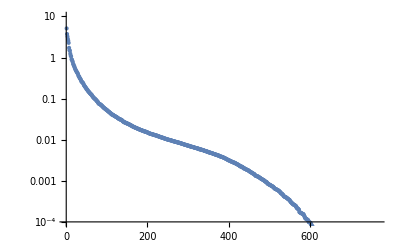

```mathematica
pcaEvals//ListLogPlot[#,PlotRange->{.0001,10}]&
```

```mathematica
ImageAdjust@*Image@*(Partition[#,28]&)/@pcaEvecs⟦;;20⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[imgToPC,imgReducePC]
imgToPC[image_Image,pcMax_Integer]:=Table[(standardizer@Flatten@ImageData@image).pcaEvecs⟦pc⟧,{pc,pcMax}]
imgToPC[pcMax_Integer]:=imgToPC[#,pcMax]&
imgReducePC[image_Image,pcMax_Integer]:=Image[Partition[imgToPC[image,pcMax]pcaEvecs⟦;;pcMax⟧,28]]
imgReducePC[pcMax_Integer]:=imgReducePC[#,pcMax]&
```

```mathematica
Table[ListPointPlot3D[
imgToPC[3]/@groupedTrainingData[i]⟦1;;1000⟧,
PlotStyle->Hue[i/10]
],{i,0,9}]//Show
```

-Graphics3D-

```mathematica
Clear[distrBoundsAndCorr]
distrBoundsAndCorr[data_]:=Module[{
min,max,
fit,corrF,μ,σ,x,xx
},
{min,max}=MinMax[data];
fit=EstimatedDistribution[(data-min)/(max-min),NormalDistribution[μ,σ]]//CDF[#,xx]&//Normal;
corrF=Function[x,Evaluate[fit/.xx->x]];

{corrF,min,max}
]
```

```mathematica
Clear[toPCAStream]
toPCAStream=Module[{min,max,corrF},
(* use the same rescaling for test, validate, and train *)
{corrF,min,max}=distrBoundsAndCorr[
Flatten@Table[imgToPC[8]/@groupedTrainingData[d]⟦;;1000⟧,{d,0,9}]
];

Function[image,corrF/@Clip[(imgToPC[image,8]-min)/(max-min),{0,1}]]
];
```

```mathematica
pcaStreams=Table[toPCAStream/@groupedTrainingData[d][[;;100]],{d,0,9}];
```

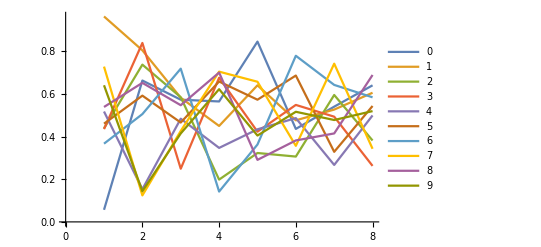

```mathematica
Mean/@pcaStreams//ListLinePlot[#,PlotLegends->Range[0,9],PlotStyle->Thick]&
```

#### Checking that value range is roughly uniform

{10,100,8}

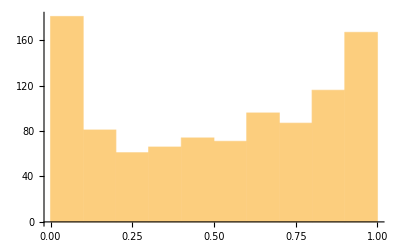
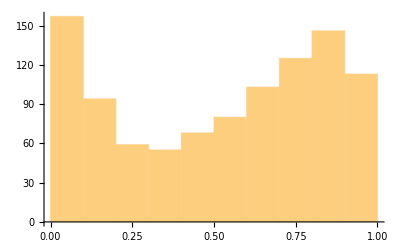
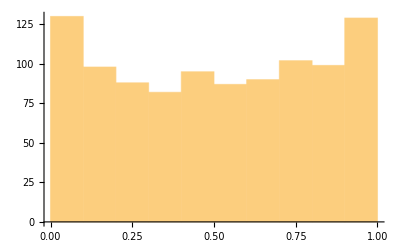
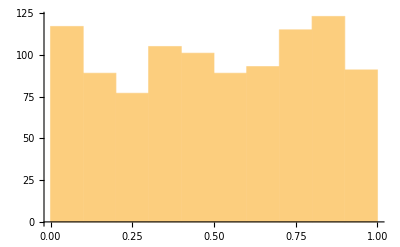
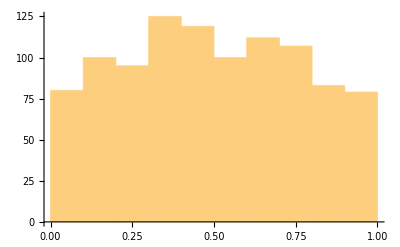
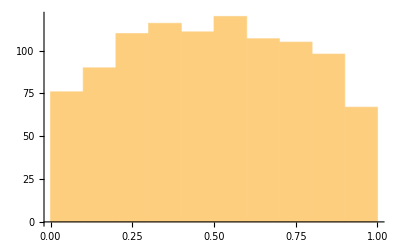
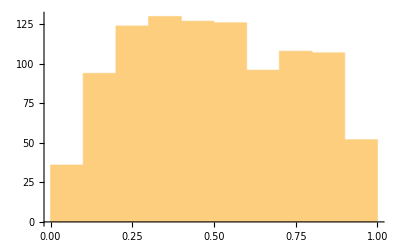
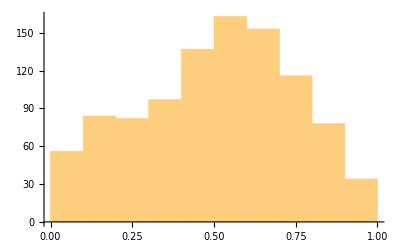

```mathematica
pcaStreams//Dimensions
Flatten[pcaStreams,{1,2}]ᵀ;
Histogram/@%
```

## t-SNE

#### Export to Python

```mathematica
Module[{d},
For[d=0,d≤9,
Export[NotebookDirectory[]<>"/data/mnist.train."<>ToString[d]<>".csv",imgToPC[30]/@groupedTrainingData[d]];
Export[NotebookDirectory[]<>"/data/mnist.validate."<>ToString[d]<>".csv",imgToPC[30]/@groupedValidationData[d]];
Export[NotebookDirectory[]<>"/data/mnist.test."<>ToString[d]<>".csv",imgToPC[30]/@groupedTestData[d]];
d++
]]
```

#### Import from Python

```mathematica
tSNEStreamRawTrain=<||>;
tSNEStreamRawValidate=<||>;
tSNEStreamRawTest=<||>;
```

```mathematica
Module[{d,dim},
For[dim=2,dim≤3,
For[d=0,d≤9,
tSNEStreamRawTrain[{d,dim}]=Import[NotebookDirectory[]<>"/data/mnist.train."<>ToString[d]<>".tSNE-"<>ToString[dim]<>".csv"];
tSNEStreamRawValidate[{d,dim}]=Import[NotebookDirectory[]<>"/data/mnist.validate."<>ToString[d]<>".tSNE-"<>ToString[dim]<>".csv"];
tSNEStreamRawTest[{d,dim}]=Import[NotebookDirectory[]<>"/data/mnist.test."<>ToString[d]<>".tSNE-"<>ToString[dim]<>".csv"];
d++
];
dim++
]]
```

```mathematica
tSNEStreamRawValidate[{0,3}][[3]]
```

{64.5167,3.93045,-23.4125}

```mathematica
tSNEStreamTrain=<||>;
tSNEStreamValidate=<||>;
tSNEStreamTest=<||>;
```

```mathematica
Module[{
d,dim,
min,max,corrF
},
For[dim=2,dim≤3,
(* use the same rescaling for test, validate, and train *)
{corrF,min,max}=distrBoundsAndCorr[
Flatten@Table[tSNEStreamRawTrain[{d,dim}],{d,0,9}]
];

For[d=0,d≤9,
tSNEStreamTrain[{d,dim}]=Map[corrF@*(Clip[#,{0,1}]&),(tSNEStreamRawTrain[{d,dim}]-min)/(max-min),{2}];
tSNEStreamValidate[{d,dim}]=Map[corrF@*(Clip[#,{0,1}]&),(tSNEStreamRawValidate[{d,dim}]-min)/(max-min),{2}];
tSNEStreamTest[{d,dim}]=Map[corrF@*(Clip[#,{0,1}]&),(tSNEStreamRawTest[{d,dim}]-min)/(max-min),{2}];
d++
];
dim++
]]
```

```mathematica
Show@@Table[
ListPointPlot3D[tSNEStreamTrain[{d,3}],PlotRange->{{0,1},{0,1}},PlotStyle->Hue[d/10]],
{d,0,9}
]
```

-Graphics3D-

```mathematica
Show@@Table[
ListPointPlot3D[tSNEStreamTest[{d,3}],PlotRange->{{0,1},{0,1}},PlotStyle->Hue[d/10]],
{d,0,9}
]
```

-Graphics3D-

#### Legacy Implementation

```mathematica
Clear[tSNEReducer,tSNEReduce]
tSNEReducer[n_Integer]:=tSNEReducer[n]=imgToPC[30]/@First/@(RandomSample[trainingData,1000])//DimensionReduction[#,n,Method->{"TSNE","Perplexity"->40}]&
tSNEReduce[img_Image,n_Integer]:=tSNEReducer[n]@imgToPC[30]@img
tSNEReduce[n_Integer]:=tSNEReduce[#,n]&
```

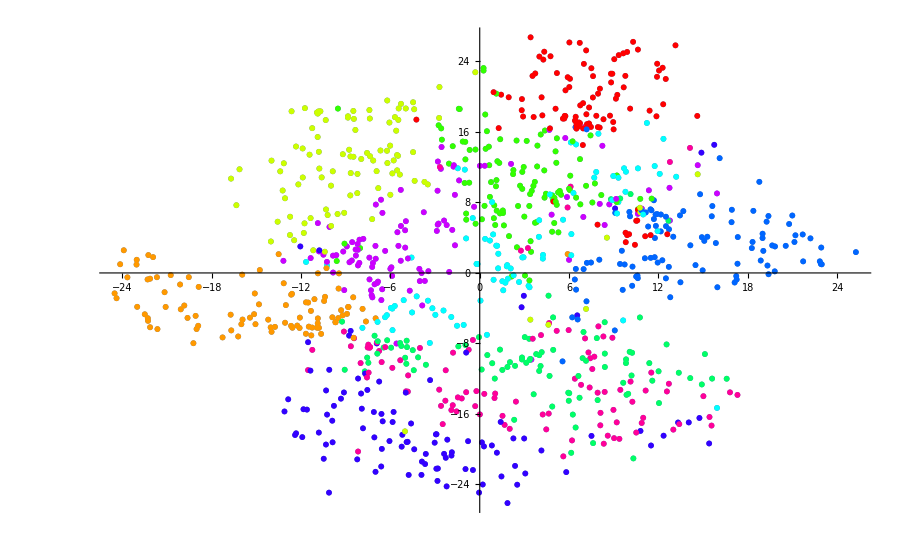

```mathematica
Module[{
data=RandomSample[trainingData,1000],
colors
},
colors=Hue[#/10]&/@(Last/@data);
ListPlot[Thread[Style[
tSNEReduce[2]/@(First/@data),
colors
]]]
]
```

```mathematica
Clear[totSNEStream]
totSNEStream[n_Integer]:=totSNEStream[n]=Module[{min,max,corrF},
(* use the same rescaling for test, validate, and train *)
{corrF,min,max}=distrBoundsAndCorr[
Flatten@Table[tSNEReduce[n]/@groupedTrainingData[d]⟦;;100⟧,{d,0,9}]
];

Function[image,corrF/@Clip[(tSNEReduce[n]@image-min)/(max-min),{0,1}]]
];
```

```mathematica
Table[
totSNEStream[d]@groupedTrainingData[2][[1]]//AbsoluteTiming//Echo,
{d,2,6}
];
```

{91.9514,{0.698373,0.225892}}

{104.57,{0.0683939,0.831355,0.742158}}

{108.843,{0.0448845,0.581871,0.978337,0.564798}}

{109.416,{0.18726,0.924398,0.174105,0.360385,0.267895}}

{110.077,{0.0340085,0.645147,0.522436,0.13955,0.601905,0.244496}}

#### Checking that value ranges are roughly uniform

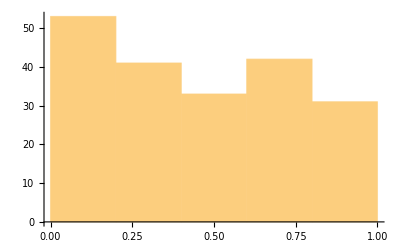
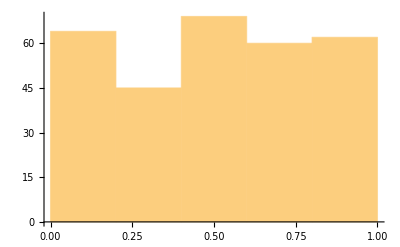
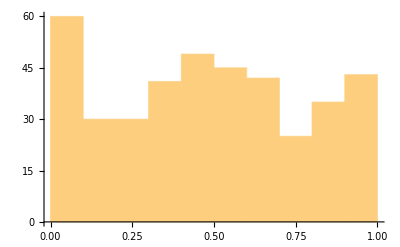
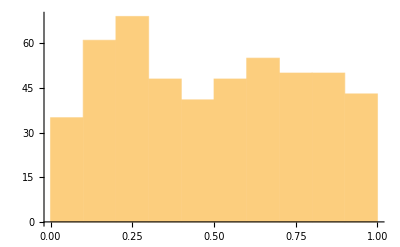
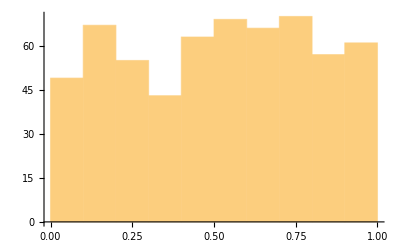

```mathematica
Table[
totSNEStream[d]/@First/@RandomSample[trainingData,100]//Flatten//Histogram,
{d,2,6}
]
```

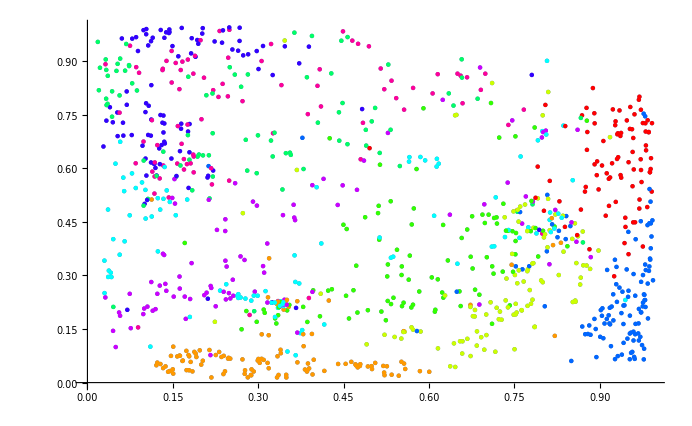

```mathematica
Module[{
data=RandomSample[trainingData,1000],
colors
},
colors=Hue[#/10]&/@(Last/@data);
ListPlot[Thread[Style[
totSNEStream[2]/@(First/@data),
colors
]]]
]
```

## Deskewing

```mathematica
Clear[moments]
moments[image_Image]:=With[{
(* we assume the image is square *)
data=ImageData@image
},

Module[{
c=ConstantArray[Range[0,Length@data-1],Length@data],
normData=data/Total@Flatten@data,
μ,M00,M11,M01
},

μ={Total[c*normData,2],Total[cᵀ*normData,2]};
M00=Total[(μ⟦1⟧-c)^2*normData,2];
M11=Total[(μ⟦2⟧-cᵀ)^2*normData,2];
M01=Total[(μ⟦1⟧-c)(μ⟦2⟧-(cᵀ))*normData,2];

{
μ,
({{M00, M01}, {M01, M11}})
}
]]

moments@groupedTrainingData[1]⟦18⟧
```

{{13.4763,13.4483},{{70.8037,-0.640574},{-0.640574,68.1555}}}

```mathematica
Clear[deskew]
deskew[image_Image]:=Module[{
μ,M,α,transform,icenter=ImageDimensions[image]/2, offset
},
{μ,M}=moments[image];
α=M⟦1,2⟧/M⟦1,1⟧*First@icenter;
transform=({{1, α}, {0, 1}});
offset=μ-transform.icenter;

ImageTransformation[image,TranslationTransform[-offset]@*AffineTransform[transform]@*TranslationTransform[offset],Background->White,Masking->All,Resampling->"Lanczos",Padding->"Fixed"]
]
```

```mathematica
{#,deskew@#}&/@groupedTrainingData[5]⟦11;;20⟧//TableForm
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

## Average Pixel Value

```mathematica
Table[{
d,Total/@(N@Flatten@ImageData@Binarize@ImageCrop[#,20]&)/@groupedTrainingData[d][[;;500]]//Mean
},
{d,0,9,1}
]
```

{{0,261.33},{1,337.78},{2,281.758},{3,287.256},{4,302.78},{5,297.69},{6,292.896},{7,312.792},{8,280.438},{9,304.418}}

## Pixel Sequence

### Images to 1D Sequence

```mathematica
Clear[MNISTPP]
MNISTPP[img_Image,res_Integer:10,angle_Integer:135]:=With[{
idata=img//ImageCrop[#,20]&//ImageResize[#,res]&//Binarize//ImageData,
rdata=img//ImageRotate[#,angle °]&//ImageCrop[#,20]&//ImageResize[#,res]&//Binarize//ImageData
},
(Flatten/@{idata,idataᵀ,rdata})ᵀ
]
MNISTPP[res_Integer,angle_Integer:135]:=MNISTPP[#,res,angle]&
```

```mathematica
centroids[[1]]//MNISTPP[5]
```

{{1,1,1},{1,1,1},{0,1,0},{0,0,1},{1,1,1},{1,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,0},{1,0,0},{0,0,1},{1,1,1},{1,1,1},{0,0,0},{0,0,0},{0,0,0},{1,1,0},{0,0,0},{1,1,1},{1,1,1},{0,0,1},{0,0,1},{1,1,1},{1,1,1}}

### Visualize Streams

```mathematica
Clear[avgDigitDiag1]
avgDigitDiag1[images_List]:=With[{
seqs=Median/@((MNISTPP[#,20]ᵀ&/@images)ᵀ)
},

plotGrid[{
ListPlot[#,Joined->True,PlotStyle->Black,Filling->Bottom,PlotRange->{0,1},AspectRatio->.05,ImageSize->700]&/@seqs
}ᵀ,
500,70,ImagePadding->14
]
]
avgDigitDiag1[digit_Integer]:=avgDigitDiag1@groupedTrainingData[digit][[;;500]]
```

### Centroids

```mathematica
centroids=ParallelTable[ImageData/@groupedTrainingData[d]//Median//Image,{d,0,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
centroidsds=ParallelTable[ImageData/@deskew/@groupedTrainingData[d]//Median//Image,{d,0,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Binarize/@centroids,Binarize/@centroidsds}//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
{#,avgDigitDiag1@{centroids⟦#+1⟧}}&/@Range[0,9]//TableForm
```

0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9 | -Graphics-

Which angle is best?

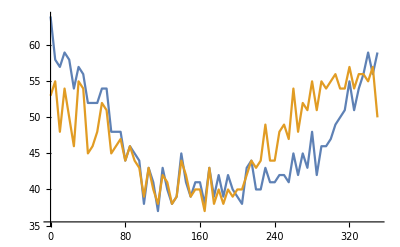
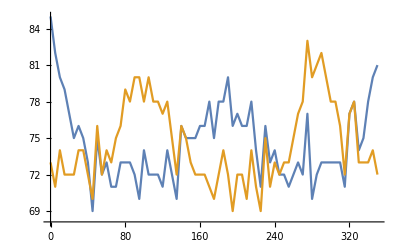

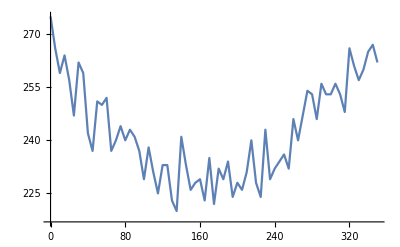

```mathematica
Table[
With[{
scanlines=MNISTPP[10,angle]/@centroidsds⟦;;2⟧
},
Table[{sᵀ⟦1⟧.sᵀ⟦3⟧,sᵀ⟦2⟧.sᵀ⟦3⟧},{s,scanlines}]
],
{angle,0,350,5}
]//Transpose[#,{2,1,3}]&;
ListLinePlot[#,DataRange->{0,350}]&/@Transpose/@%
ListLinePlot[#,DataRange->{0,350}]&@Total@Total[Transpose/@%%]
```

```mathematica
Export[NotebookDirectory[]<>"mnist-centroids.csv",Map[FromDigits[#,2]&,MNISTPP[10]/@centroids,{2}]]
Export[NotebookDirectory[]<>"mnist-centroids-deskewed.csv",Map[FromDigits[#,2]&,MNISTPP[10]/@centroidsds,{2}]]
Export[NotebookDirectory[]<>"mnist-centroids-deskewed-large.csv",Map[FromDigits[#,2]&,MNISTPP[20]/@centroidsds,{2}]]
```

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-centroids.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-centroids-deskewed.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-centroids-deskewed-large.csv

### Centroids Annealing Schedule

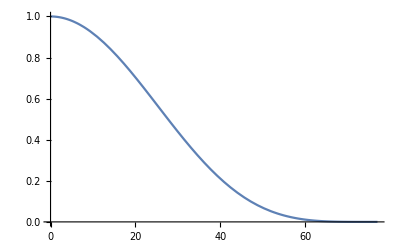

```mathematica
Plot[Cos[(10x/77)/(2π)]^4,{x,0,77}]
```

### Sequence Analysis

```mathematica
{#,avgDigitDiag1[#]}&/@Range[0,9]//TableForm
```

0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9 | -Graphics-

## Dataset Export

cropped to 20 x 20
downscaled to 10 x 10
streams: flattened, flattened transposed, and flattened rotated

```mathematica
Table[
Module[{n},For[n=0,n≤9,
Print@Export[
NotebookDirectory[]<>#1,
Map[FromDigits[#,2]&,#2,{2}],
"CSV"
]&@@@({
{
"mnist-simple-"<>ToString[n]<>what["name"]<>"-train.csv",
"mnist-simple-"<>ToString[n]<>what["name"]<>"-validate.csv",
"mnist-simple-"<>ToString[n]<>what["name"]<>"-test.csv"
},
Map[what["fn"],{
groupedTrainingData[n],
groupedValidationData[n],
groupedTestData[n]
},{2}]
}ᵀ);

n++
]],
{what,{
<|"name"->"","fn"->MNISTPP[10]|>,
<|"name"->"-deskewed","fn"->MNISTPP[10]@*deskew|>,
<|"name"->"-deskewed-large","fn"->MNISTPP[20]@*deskew|>
}}
];
```

## PCA Data

```mathematica
Table[
Module[{n},For[n=0,n≤9,
Print@Export[
NotebookDirectory[]<>#1,
#2,
"CSV"
]&@@@({
{
"mnist-"<>what["name"]<>"-"<>ToString[n]<>"-train.csv",
"mnist-"<>what["name"]<>"-"<>ToString[n]<>"-validate.csv",
"mnist-"<>what["name"]<>"-"<>ToString[n]<>"-test.csv"
},
Map[what["fn"],{
groupedTrainingData[n],
groupedValidationData[n],
groupedTestData[n]
},{2}]
}ᵀ);

n++
]],
{what,{
<|"name"->"pca-8bit","fn"->(Round@*((#*255.998-.499)&)@*toPCAStream)|>
}}
]
```

$Aborted

```mathematica
totSNEStream[2]
```

$Aborted

## tSNE Data

```mathematica
Table[
Module[{n},For[n=0,n≤9,
Print@Export[
NotebookDirectory[]<>#1,
#2,
"CSV"
]&@@@({
{
"mnist-"<>what["name"]<>"-"<>ToString[n]<>"-train.csv",
"mnist-"<>what["name"]<>"-"<>ToString[n]<>"-validate.csv",
"mnist-"<>what["name"]<>"-"<>ToString[n]<>"-test.csv"
},
what["fn"]@@@{
{tSNEStreamTrain,n},
{tSNEStreamValidate,n},
{tSNEStreamTest,n}
}
}ᵀ);

n++
]],
{what,{
<|
"name"->"tsne-2",
"fn"->Function[{stream,d},
Round@((#*255.998-.499)&)@stream[{d,2}]
]
|>,
<|
"name"->"tsne-3",
"fn"->Function[{stream,d},
Round@((#*255.998-.499)&)@stream[{d,3}]
]
|>
}}
]
```

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-0-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-0-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-0-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-1-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-1-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-1-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-2-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-2-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-2-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-3-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-3-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-3-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-4-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-4-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-4-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-5-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-5-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-5-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-6-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-6-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-6-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-7-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-7-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-7-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-8-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-8-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-8-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-9-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-9-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-2-9-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-0-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-0-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-0-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-1-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-1-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-1-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-2-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-2-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-2-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-3-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-3-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-3-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-4-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-4-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-4-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-5-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-5-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-5-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-6-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-6-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-6-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-7-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-7-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-7-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-8-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-8-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-8-test.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-9-train.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-9-validate.csv

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\mnist-tsne-3-9-test.csv

{Null,Null}

## Miscellaneous

```mathematica
ToString/@RandomInteger[{25000,35000},30]//StringRiffle[#," "]&
```

29885 27489 31509 25388 27175 32030 31615 30680 34899 25969 32780 30084 33470 26845 32630 28785 30883 26159 30762 34317 26305 33016 29421 25127 33282 33391 34143 31087 30698 27968

```mathematica
Map[(Round@*((#*255.998-.499)&)@*toPCAStream),
groupedTrainingData/@Range[0,9],
{2}
]//MinMax
```

{0,255}

```mathematica
1*255.999-.498
```

255.501